# info-graphics

```mathematica
imagedir=FileNameJoin[{NotebookDirectory[],"images\\"}];
SetDirectory[imagedir];
```

```mathematica
xnum=ynum=10;
```

```mathematica
num = √(xnum ynum); 
atom[i_,excited_]:=If[excited,Graphics[{Orange,Disk[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}]];
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
gridpts = Table[atom[i,False],{i,Range[num^2]}];
```

```mathematica
atomGraphic = Join[Table[Graphics3D[{Orange,Sphere[{i,j,0},0.1]}],{i,1,xnum},{j,1,ynum}],Table[Graphics3D[{Red,Arrow[{{i,j,-0.5},{i,j,0.5}}]}],{i,1,xnum},{j,1,ynum}]];
```

```mathematica
graphic =Show[atomGraphic,Boxed-> False]
```

-Graphics3D-

```mathematica
depth=5;
atomGraphic = Table[Graphics3D[{Orange,Sphere[{i,j,k},0.1]}],{i,1,xnum},{j,1,ynum},{k,1,depth}];
```

```mathematica
graphic=Show[atomGraphic,Boxed->False]
```

-Graphics3D-

```mathematica
Export[ToString[StringForm["graphic_3D_atom_dipoles_``x``x``.png",xnum,ynum,depth]],graphic,ImageResolution-> 300]
```

graphic_3D_atom_dipoles_10x10x5.png

```mathematica
reds = Table[Hue[1,1.0/(1+(0.5i)^2)],{i,{-2,-1,0,1,2}}]
```

{Hue[1, 0.5],Hue[1, 0.8],Hue[1, 1.],Hue[1, 0.8],Hue[1, 0.5]}

```mathematica
plts=Table[Plot[{2 √(1+z^2)-10i,-2 √(1+z^2)-10i},{z,-5,5},PlotStyle->Hue[1,1./(1+(0.5i)^2)],Filling->{1-> {2}},Axes->False,PlotRange->{-50,50},ImageSize->Large],{i,{-2,-1,0,1,2}}];
AppendTo[plts,Plot[Evaluate[{If[z>0,0.8*2 √(1+z^2)-10i],If[z>0,-0.8*2 √(1+z^2)-10i]}/.i-> 1],{z,-5,5},PlotStyle->Hue[0.54,1],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
AppendTo[plts,Plot[Evaluate[{If[z<=0,0.8*2 √(1+z^2)-10i],If[z<=0,-0.8*2 √(1+z^2)-10i]}/.i-> 1],{z,-5,5},PlotStyle->Hue[1,0.8],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
```

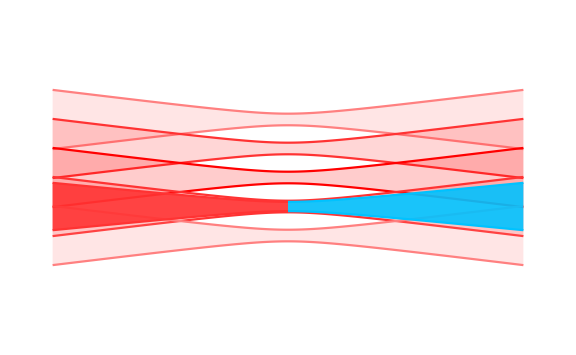

```mathematica
plt =Show[plts,ImageSize-> Large]
```

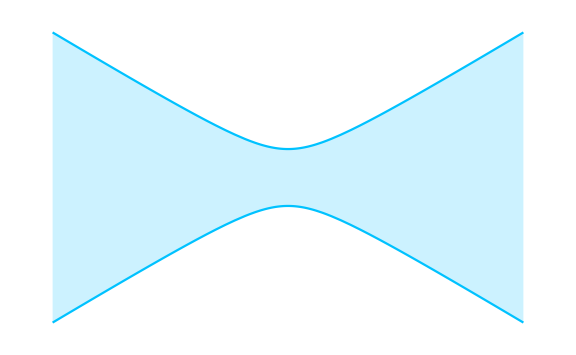

```mathematica
Plot[{2 √(1+z^2)-10,-2 √(1+z^2)-10},{z,-5,5},PlotStyle->Hue[0.54,1],Filling->{1-> {2}},Axes->False,ImageSize->Large]
```

```mathematica
Export["FORT_sites.png",plt,ImageResolution-> 600]
```

FORT_sites.png

```mathematica
ColorData["DarkRainbow"][[-1]][0.9]
```

RGBColor[0.72987, 0.239399, 0.230961]

```mathematica
Hue[0.54,0.8]
```

Hue[0.54, 0.8]

```mathematica
Hue[1,0.8]
```

Hue[1, 0.8]

```mathematica
1.7*^9/10
```

1.7×10^8

```mathematica
{{-2,1},{-1,1},{-1,0.3},{1,0.3},{1,1},{1,2}}
```

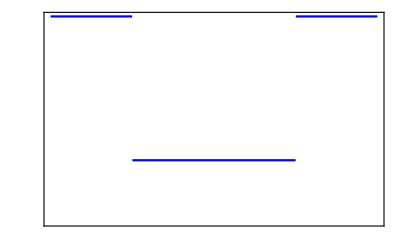

```mathematica
plt=Plot[Piecewise[{{1,x<-1},{0.3,-1<=x≤1},{1,x>1}}],{x,-2,2},Frame->{True,True,False,False},Axes-> False,PlotRange->{0,1},FrameTicks->None,PlotStyle->Blue]
```

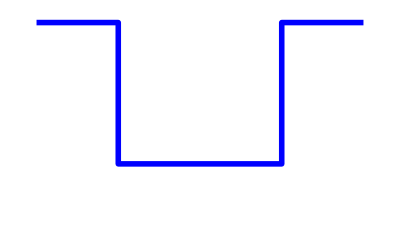

```mathematica
plt=ListPlot[{{-2,1},{-1,1},{-1,0.3},{1,0.3},{1,1},{1,1},{2,1}},Frame->{False,False,False,False},Axes-> False,PlotRange->{0,1},FrameTicks->None,PlotStyle->Directive[Blue,AbsoluteThickness[4]],Joined->True]
```

```mathematica
Export["sq_pulse_thick4.png",plt,ImageResolution-> 300]
```

sq_pulse_thick4.png

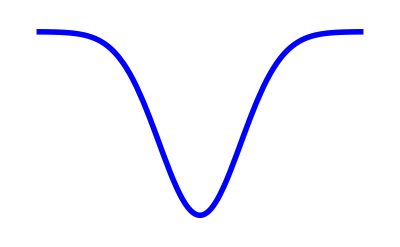

```mathematica
plt=Plot[1-Exp[-2 x^2],{x,-2,2},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Blue,AbsoluteThickness[4]]]
```

```mathematica
Export["minus_gaussian_thick4.png",plt,ImageResolution-> 300]
```

minus_gaussian_thick4.png

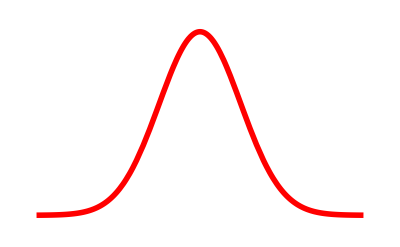

```mathematica
plt=Plot[Exp[-2 x^2],{x,-2,2},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Red,AbsoluteThickness[4]]]
```

```mathematica
Export["gaussian_thick4.png",plt,ImageResolution-> 300]
```

gaussian_thick4.png

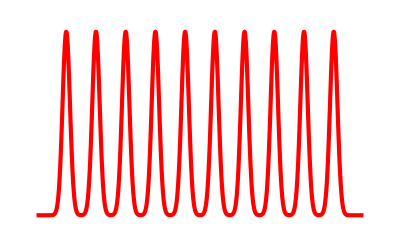

```mathematica
plt=Plot[Sum[Exp[-2(x-4 (j-1))^2],{j,Range[10]}],{x,-4,2*20},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Red,AbsoluteThickness[3]]]
```

```mathematica
Export["gaussian_array10_thick3.png",plt,ImageResolution-> 300]
```

gaussian_array10_thick3.png

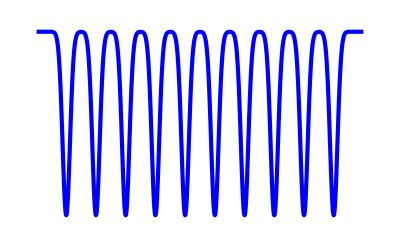

```mathematica
plt=Plot[1-Sum[Exp[-2(x-4 (j-1))^2],{j,Range[10]}],{x,-4,2*20},Frame->{False,False,False,False},Axes-> False,PlotRange->{-0.05,1.05},FrameTicks->None,PlotStyle->Directive[Blue,AbsoluteThickness[3]]]
```

```mathematica
Export["minus_gaussian_array10_thick3.png",plt,ImageResolution-> 300]
```

minus_gaussian_array10_thick3.png

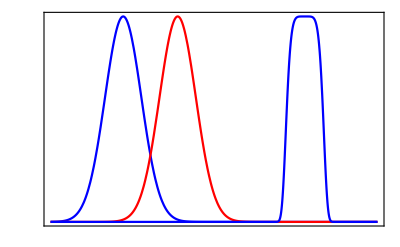

```mathematica
plt=Plot[{Exp[-2 x^2],Exp[-2(x-1.5)^2],Exp[-40(x-5)^6]},{x,-2,7},Frame->{True,True,False,False},Axes-> False,PlotRange->{0,1},FrameTicks->None,PlotStyle->{Blue,Red}]
```

```mathematica
Export["stirap_excitation_stim_pulses.png",plt,ImageResolution-> 300]
```

stirap_excitation_stim_pulses.png